```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
TestForAll[rs:<|"Index"->_,"QCode"->_,"RuleSet"->_|>] := Module[{ans}, 
If[Length[ans=TestForConflictingRules[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloIdentityRule[rs]]>0,Return[ans]];
If[Length[ans=TestForRenamedRuleSet[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloInitialSubstringRule[rs]]>0,Return[ans]];
If[Length[ans=TestForUnbalancedRuleSet[rs]]>0,Return[ans]];
Return[TestForShorteningRuleSet[rs]]
];
```

```mathematica
rs=FromReducedRankIndex[1]
```

<|Index→1,QCode→,RuleSet→{A→}|>

Function to perform loops

```mathematica
doEnumerate[start_Integer, stop_Integer, lookfor_List, keep_(True|False)] :=
```

Probabilistic functions:

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
Print["len: ",len];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% of rules used, tally the rest *)
Print["ruletally: ",ruletally];
least=First@First@SortBy[ruletally,Last];  
Print["least: ",least];
(* identify the least used rule *)
Flatten@Position[ru,least] 
];
```

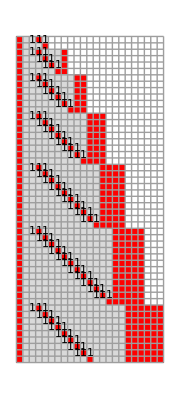


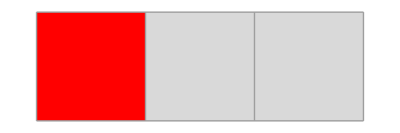
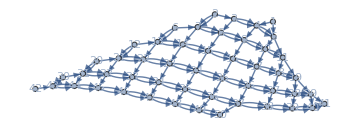
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssF2FF=SSS[{"ABA"->"AAB",""->"BAA"},"BAABA",50,SSSSize->Small,NetSize->Medium];
```

```mathematica
sssF2FF["RulesUsed"]
```

{1,2,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1}

```mathematica
LeastUsedRulePositions[sssF2FF]
```

len: 50

ruletally: {{1,41},{2,5}}

least: 2

{2,6,12,20,30,42}

```mathematica
CheckDimension[%16]
```

{failed,2 | 6 | 12 | 20 | 30 | 42
4 | 6 | 8 | 10 | 12 | 
2 | 2 | 2 | 2 |  | }